```mathematica
沿z轴的电场分布
```

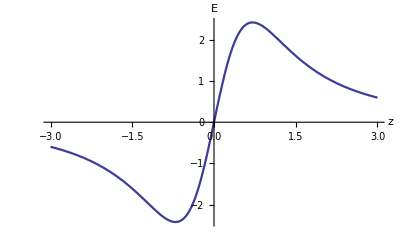

```mathematica
R=1;a=R^2+z^2+ρ^2;b=2ρ*R;
V[z_,ρ_]:=(2 EllipticK[(2 b)/(-a+b)])/(√(a-b))+(2 EllipticK[(2 b)/(a+b)])/(√(a+b));
field=-D[V[z,ρ],z]/.ρ->0;
Plot[field,{z,-3R,3R},
AxesLabel->{"z","E"},
AxesStyle->Thickness[0.003],
PlotStyle->Thickness[0.004],
BaseStyle->{FontSize->13}]
Clear[R,a,b,V,field]
```